```mathematica
l=Import["l_force.dat","Table"]
```

{{0.0916091,0.0913394,0.0913182,0.0907939,0.0912364,0.0912242,0.0919727,0.0935879,0.0925242,0.0923394,0.0926606,179,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},198,{}}
 |  |  |  |

```mathematica
l[[99]]
```

{0.0914977,0.0914418,0.0915347,0.0915725,0.0916801,0.0916459,0.092028,0.0921321,0.0924085,0.0927699,0.0931453,0.0939025,0.0938325,0.128576,0.129581,0.205886,0.234884,0.315162,0.427184,0.636078,0.617617,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ltab=Table[{2n,l[[99]][[n+1]]}, {n,0,20}]
```

{{0,0.0914977},{2,0.0914418},{4,0.0915347},{6,0.0915725},{8,0.0916801},{10,0.0916459},{12,0.092028},{14,0.0921321},{16,0.0924085},{18,0.0927699},{20,0.0931453},{22,0.0939025},{24,0.0938325},{26,0.128576},{28,0.129581},{30,0.205886},{32,0.234884},{34,0.315162},{36,0.427184},{38,0.636078},{40,0.617617}}

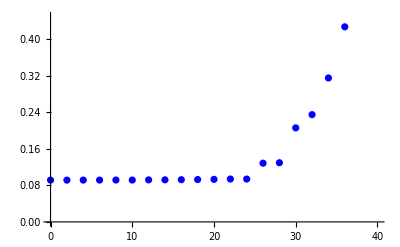

```mathematica
lplot=ListPlot[ltab,PlotStyle->Blue]
```

```mathematica
Export["l_force_py.dat",ltab]
```

l_force_py.dat

```mathematica
f=Import["f_force.dat","Table"]
```

{1}
 |  |  |  |

```mathematica
f[[99]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.06,0.04,0.18,0.22,0.350909,0.458182,0.68,0.675152,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ftab=Table[{2n,f[[99]][[n+1]]},{n,0,20}]
```

{{0,0.},{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.},{14,0.},{16,0.},{18,0.},{20,0.},{22,0.},{24,0.},{26,0.06},{28,0.04},{30,0.18},{32,0.22},{34,0.350909},{36,0.458182},{38,0.68},{40,0.675152}}

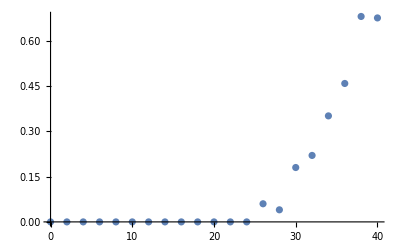

```mathematica
fplot= ListPlot[ftab,PlotStyle->Teal]
```

```mathematica
Export["f_force_py.dat",ftab]
```

f_force_py.dat

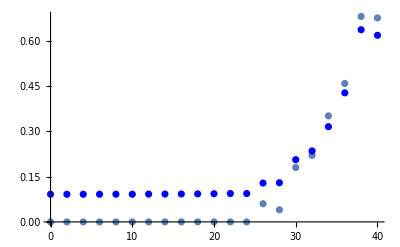

```mathematica
Show[fplot,lplot]
```

```mathematica
h= Import["h_force.dat","Table"]
```

{1}
 |  |  |  |

```mathematica
h[[99]]
```

{3.39215,3.43304,3.47404,3.51566,3.55755,3.59962,3.64205,3.68461,3.72769,3.77106,3.81431,3.85837,3.90241,3.99616,4.04382,4.21122,4.30879,4.49416,4.74165,5.16404,5.18873,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
htab=Table[{2n,h[[99]][[n+1]]},{n,0,20}]
```

{{0,3.39215},{2,3.43304},{4,3.47404},{6,3.51566},{8,3.55755},{10,3.59962},{12,3.64205},{14,3.68461},{16,3.72769},{18,3.77106},{20,3.81431},{22,3.85837},{24,3.90241},{26,3.99616},{28,4.04382},{30,4.21122},{32,4.30879},{34,4.49416},{36,4.74165},{38,5.16404},{40,5.18873}}

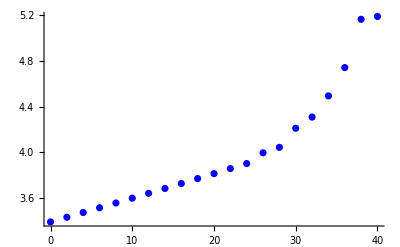

```mathematica
hplot = ListPlot[htab,PlotStyle->Blue]
```

```mathematica
Export["h_force_py.dat",htab]
```

h_force_py.dat

```mathematica
(* Invert h(force) to force(h) to obtain force- extension relation *)
```

```mathematica
forcetab = Table[{h[[99]][[n+1]],2n},{n,0,20}]
```

{{3.39215,0},{3.43304,2},{3.47404,4},{3.51566,6},{3.55755,8},{3.59962,10},{3.64205,12},{3.68461,14},{3.72769,16},{3.77106,18},{3.81431,20},{3.85837,22},{3.90241,24},{3.99616,26},{4.04382,28},{4.21122,30},{4.30879,32},{4.49416,34},{4.74165,36},{5.16404,38},{5.18873,40}}

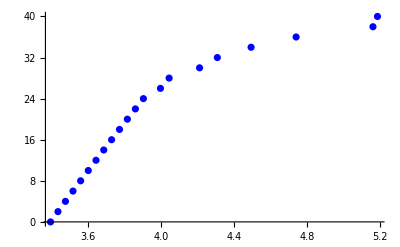

```mathematica
forceplot = ListPlot[forcetab,PlotStyle->Blue]
```

```mathematica
Export["force_extension_py.dat", forcetab]
```

force_extension_py.dat

```mathematica
theta = Import["theta_force.dat","Table"]
```

{1}
 |  |  |  |

```mathematica
theta[[99]]
```

{0.57725,0.574621,0.571962,0.569186,0.566263,0.563347,0.56028,0.557157,0.553878,0.55048,0.547051,0.543367,0.53976,0.524845,0.520337,0.489779,0.474497,0.440512,0.393297,0.309034,0.30934,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
thetatab= Table[{2n,theta[[99]][[n+1]]},{n,0,20}]
```

{{0,0.57725},{2,0.574621},{4,0.571962},{6,0.569186},{8,0.566263},{10,0.563347},{12,0.56028},{14,0.557157},{16,0.553878},{18,0.55048},{20,0.547051},{22,0.543367},{24,0.53976},{26,0.524845},{28,0.520337},{30,0.489779},{32,0.474497},{34,0.440512},{36,0.393297},{38,0.309034},{40,0.30934}}

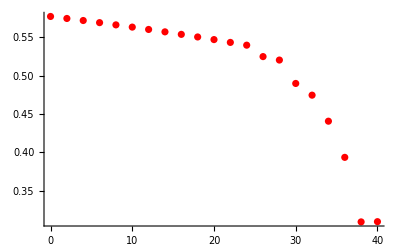

```mathematica
thetaplot = ListPlot[thetatab,PlotStyle->Red]
```

```mathematica
Export["theta_force_py.dat",thetatab]
```

theta_force_py.dat

```mathematica
nbub = Import["nbub_force.dat", "Table"]
```

{1}
 |  |  |  |

```mathematica
nbub[[99]]
```

{2.21553,2.21348,2.21323,2.2146,2.21626,2.21301,2.21785,2.21856,2.2206,2.22691,2.22988,2.23634,2.23978,2.19711,2.20124,2.09996,2.06833,1.95419,1.79931,1.49295,1.5272,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
nbubtab = Table[{2n,nbub[[99]][[n+1]]},{n,0,20}]
```

{{0,2.21553},{2,2.21348},{4,2.21323},{6,2.2146},{8,2.21626},{10,2.21301},{12,2.21785},{14,2.21856},{16,2.2206},{18,2.22691},{20,2.22988},{22,2.23634},{24,2.23978},{26,2.19711},{28,2.20124},{30,2.09996},{32,2.06833},{34,1.95419},{36,1.79931},{38,1.49295},{40,1.5272}}

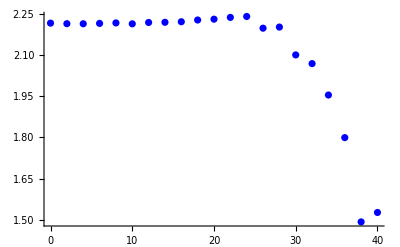

```mathematica
nbubplot = ListPlot[nbubtab,PlotStyle->Blue]
```

```mathematica
Export["nbub_force_py.dat",nbubtab]
```

nbub_force_py.dat

```mathematica
bubsize = Import["bubsize_force.dat","Table"]
```

{1}
 |  |  |  |

```mathematica
bubsize[[99]]
```

{1.27617,1.27677,1.27807,1.27836,1.27861,1.27967,1.28451,1.28488,1.28918,1.29191,1.29573,1.30691,1.3021,2.49108,2.51702,5.16707,6.17141,8.97531,12.8987,20.2378,19.5791,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
bubsizetab = Table[{2n,bubsize[[99]][[n+1]]},{n,0,20}]
```

{{0,1.27617},{2,1.27677},{4,1.27807},{6,1.27836},{8,1.27861},{10,1.27967},{12,1.28451},{14,1.28488},{16,1.28918},{18,1.29191},{20,1.29573},{22,1.30691},{24,1.3021},{26,2.49108},{28,2.51702},{30,5.16707},{32,6.17141},{34,8.97531},{36,12.8987},{38,20.2378},{40,19.5791}}

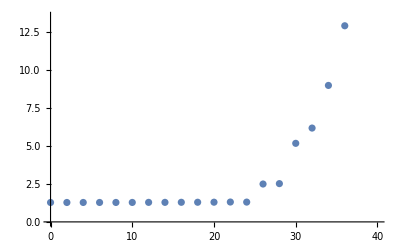

```mathematica
bubsizeplot = ListPlot[bubsizetab,PlotStyle->Teal]
```

```mathematica
Export["bubsize_force_py.dat",bubsizetab]
```

bubsize_force_py.dat

```mathematica
(* y-plots will not be used *)
y = Import["y_force.dat", "Table"]
```

{{0.0753672,0.0753738,0.0755614,0.075263,0.0755626,0.0752177,0.0760374,0.0767386,0.0766222,0.0770964,0.0768244,179,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},198,{}}
 |  |  |  |

```mathematica
y[[99]]
```

{0.0755537,0.0754999,0.0756159,0.0756307,0.0757578,0.0757009,0.0759605,0.0761013,0.0763523,0.0765563,0.0768552,0.0777272,0.0773062,0.262976,0.274064,0.720593,0.914239,1.42524,2.16796,3.55816,3.49589,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ytab = Table[{2n,y[[99]][[n+1]]},{n,0,20}]
```

{{0,0.0755537},{2,0.0754999},{4,0.0756159},{6,0.0756307},{8,0.0757578},{10,0.0757009},{12,0.0759605},{14,0.0761013},{16,0.0763523},{18,0.0765563},{20,0.0768552},{22,0.0777272},{24,0.0773062},{26,0.262976},{28,0.274064},{30,0.720593},{32,0.914239},{34,1.42524},{36,2.16796},{38,3.55816},{40,3.49589}}

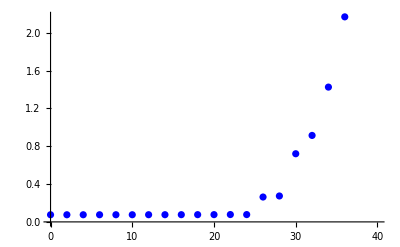

```mathematica
yplot = ListPlot[ytab,PlotStyle->Blue]
```